# Лабораторная работа по оптической микроскопии

Московский физико-технический институт (государственный университет)

Нехаев Александр, Семкин Валентин, Марголин Илья, Александров Михаил, Серягина Екатерина

13.09.2019

## Введение

### Цель работы

Получить четкие изображения предложенных образцов рельефных структур с максимальным увеличением. Сделать снимки с UV фильтром и без него. Проанализировать снимки, сделать вывод о достигнутом максимальном разрешении (по Рэлею) в обоих случаях.

Получить четкие изображения тех же структур в режиме Dark Field с объективами x100, сделать снимки структур, оценить разрешение в режиме Dark Field по снимкам.

В режиме Dark Field получить четкое изображение плоской поверхности образца с объективом x10, сделать снимок, по снимку определить число частиц загрязнения. Построить гистограмму распределения по размерам частиц.

Получить четкое Dic изображение структуры с наименьшим разрешимым периодом, подобрать положение поляризатора для оптимального разрешения. Сделать снимок. По снимку определить разрешение, период и скважность структуры.

## Ход работы

Полученные изображения структур:

```mathematica
(*Initialization section*)
SetDirectory[NotebookDirectory[]];
SetDirectory[".\\2019-09-10"];
(*Dataset*)
Dataset[
<|"x100 BF without UV"->
<|
"T500 16-55-22"-> Import["1_x100_BF.png"],"T250nm_14-38-08"-> Import["1_1_x100_BF.png"],
"D500 15-39-57"-> Import["1_2_x100_BF.png"]
|>,
"x100 BF UV"->
<|"T500 16-55-22"-> Import["1_x100_BF_UV.png"],"T250nm_14-38-08"-> Import["1_1_x100_BF_UV.png"],
"D500 15-39-57"-> Import["1_2_x100_BF_UV.png"]
|>,
"x100 DF"-> 
<|
"T500 16-55-22"-> Import["2_x100_DF.png"],
"T250nm_14-38-08"-> Import["2_1_x100_DF.png"],
"D500 15-39-57"-> Import["2_2_x100_DF.png"]
|>,
"x100 BF DIC"->
<|
"T500 16-55-22"-> Import["4_x100_BF_DIC.png"],
"T250nm_14-38-08"-> Import["4_1_x100_BF_DIC.png"],
"D500 15-39-57"-> Import["4_2_x100_BF_DIC.png"]
|>
|>
]
```

Dataset[<>]

### Определение максимального достигнутого разрешения по Рэлею

Получили изображение структур T500 16-55-22, T250nm_14-38-08 и D500 15-39-57 на поверхности используемого образца.

-Graphics-

Снимок структуры T500 16-55-22 в режиме светлого поля без UV фильтра

-Graphics-

Снимок структуры T250nm_14-38-08 в режиме светлого поля без UV фильтра

-Graphics-

Снимок структуры D500 15-39-57 в режиме светлого поля без UV фильтра

Получили изображение тех же структур, но с UV фильтром

-Graphics-

Снимок структуры T500 16-55-22 в режиме светлого поля c UV фильтром

-Graphics-

Снимок структуры T250nm_14-38-08 в режиме светлого поля c UV фильтром

-Graphics-

Снимок структуры D500 15-39-57 в режиме светлого поля c UV фильтром

Из снимков видно, что все изображения получились разрешенными. Далее будем подробнее рассматривать структуру T500 16-55-22.

#### Критерий Рэлея

Критерий Рэлея:

Для того, чтобы два источника были различимы необходимо чтобы расстояние между центрами дифракционных пятен было не меньше радиуса одного пятна.

Рассмотрим фрагменты изображений с рельефными структурами

```mathematica
(*Work itself*)
img1BF=Import["1_x100_BF.png"];
img1BFUV=Import["1_x100_BF_UV.png"];
img1BFTrimmed=ImageAdjust[Image[ImageData[ImageTrim[img1BF,{{1150,563},{1164+196,563+105}}]][[All,All,2]]
]]
img1BFUVTrimmed=ImageAdjust[
Image[ImageData[ImageTrim[img1BFUV,{{850,563},{904+196,563+105}}]][[All,All,3]]
]]
```

-Graphics-

-Graphics-

Так же введем коэффициент, для определения размеров объектов (μm/pixel) исходя из размеров метки масштаба на исходном изображении:

```mathematica
scaleExp1=ImageTrim[Import["1_x100_BF.png"],{{1884,20},{2028,60}}];
scalingCoefExp1 = Quantity[5, "Micrometers"]/ImageDimensions[scaleExp1][[1]]
```

5/146 µm

Построим срез в профиль и попытаемся аппроксимировать два соседних пика на каждом их снимков:

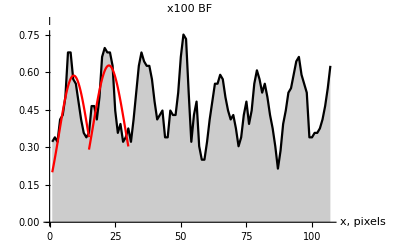

Левый пик:  | Estimate | Standard Error | t-Statistic | P-Value
a | 0.585983 | 0.0275743 | 21.251 | 6.86077×10^-11
b | 8.18246 | 0.325936 | 25.1045 | 9.67705×10^-12
c | 5.57616 | 0.469122 | 11.8864 | 5.37631×10^-8

Правый пик:  | Estimate | Standard Error | t-Statistic | P-Value
a | 0.62637 | 0.033735 | 18.5673 | 9.68216×10^-11
b | 7.6067 | 0.430596 | 17.6655 | 1.80746×10^-10
c | 6.13342 | 0.622217 | 9.85736 | 2.12506×10^-7

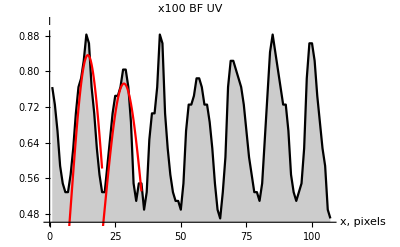

Левый пик:  | Estimate | Standard Error | t-Statistic | P-Value
a | 0.836199 | 0.012764 | 65.5121 | 1.29976×10^-15
b | 7.55996 | 0.132645 | 56.9939 | 5.99074×10^-15
c | 6.39494 | 0.232304 | 27.5283 | 1.69703×10^-11

Правый пик:  | Estimate | Standard Error | t-Statistic | P-Value
a | 0.772522 | 0.0191905 | 40.2554 | 4.93732×10^-15
b | 8.32021 | 0.269118 | 30.9166 | 1.4763×10^-13
c | 7.71753 | 0.495956 | 15.5609 | 8.76968×10^-10

```mathematica
(*Preparing slices*)
img1BFSlice=1-ImageData[img1BFTrimmed][[All,160]];
img1BFUVSlice=1-ImageData[img1BFUVTrimmed][[All,160]];
(*Setting up fitting parts*)
(*Frame corners for simple*)
f1LS=1;
f1RS=15;
f2LS=15;
f2RS=30;
(*Frame corners for UV*)
f1LUV=7;
f1RUV=20;
f2LUV=20;
f2RUV=35;
(*Cutting parts*)
img1BFSliceApproxPart1=img1BFSlice[[f1LS;;f1RS]];
img1BFUVTrimmedApproxPart1=img1BFUVSlice[[f1LUV;;f1RUV]];
img1BFSliceApproxPart2=img1BFSlice[[f2LS;;f2RS]];
img1BFUVTrimmedApproxPart2=img1BFUVSlice[[f2LUV;;f2RUV]];
(*Finding fit*)
img1BFSliceApproxPart1Fit=NonlinearModelFit[img1BFSliceApproxPart1,a Exp[-(x-b)^2/(2 c^2)],{a,b,c},x];
img1BFUVTrimmedApproxPart1Fit=NonlinearModelFit[img1BFUVTrimmedApproxPart1,a Exp[-(x-b)^2/(2 c^2)],{a,b,c},x];
img1BFSliceApproxPart2Fit=NonlinearModelFit[img1BFSliceApproxPart2,a Exp[-(x-b)^2/(2 c^2)],{a,b,c},x];
img1BFUVTrimmedApproxPart2Fit=NonlinearModelFit[img1BFUVTrimmedApproxPart2,a Exp[-(x-b)^2/(2 c^2)],{a,b,c},x];
(*Plotting slices with fits*)
(*Moving functions*)
img1BFSliceApproxPart1FitEq=img1BFSliceApproxPart1Fit["BestFit"]/.x->(x-f1LS);
img1BFUVTrimmedApproxPart1FitEq=img1BFUVTrimmedApproxPart1Fit["BestFit"]/.x->(x-f1LUV);
img1BFSliceApproxPart2FitEq=img1BFSliceApproxPart2Fit["BestFit"]/.x->(x-f2LS);
img1BFUVTrimmedApproxPart2FitEq=img1BFUVTrimmedApproxPart2Fit["BestFit"]/.x->(x-f2LUV);
(*Simple photo*)
Show[
ListPlot[img1BFSlice,PlotLabel->"x100 BF",Joined->True,PlotMarkers->None,Filling->Bottom,AxesLabel->{"x, pixels","I"}],(*Drawing slice*)
Plot[img1BFSliceApproxPart1FitEq,{x,f1LS,f1RS},PlotStyle->Red],(*Drawing left peak*)
Plot[img1BFSliceApproxPart2FitEq,{x,f2LS,f2RS},PlotStyle->Red](*Drawing right peak*)
]
(*Printnig fit data*)
Print["Левый пик: ",img1BFSliceApproxPart1Fit["ParameterTable"]]
Print["Правый пик: ",img1BFSliceApproxPart2Fit["ParameterTable"]]
(*UV Photo*)
Show[
ListPlot[img1BFUVSlice,PlotLabel->"x100 BF UV",Joined->True,PlotMarkers->None,Filling->Bottom,AxesLabel->{"x, pixels","I"}],(*Drawing slice*)
Plot[img1BFUVTrimmedApproxPart1FitEq,{x,f1LUV,f1RUV},PlotStyle->Red],(*Drawing left peak*)
Plot[img1BFUVTrimmedApproxPart2FitEq,{x,f2LUV,f2RUV},PlotStyle->Red](*Drawing right peak*)
]
(*Printnig fit data*)
Print["Левый пик: ",img1BFUVTrimmedApproxPart1Fit["ParameterTable"]]
Print["Правый пик: ",img1BFUVTrimmedApproxPart2Fit["ParameterTable"]]
```

Таким образом, получаем расстояния между указанными пиками для изображения без UV-фильтра:

```mathematica
peak1S=Around[(b/.img1BFSliceApproxPart1Fit["BestFitParameters"])+f1LS,img1BFSliceApproxPart1Fit["ParameterErrors"][[2]]];
peak2S=Around[(b/.img1BFSliceApproxPart2Fit["BestFitParameters"])+f2LS,img1BFSliceApproxPart2Fit["ParameterErrors"][[2]]];
TS=(peak2S-peak1S)*scalingCoefExp1
```

(0.4600.018) µm

Для пиков на снимке без UV-фильтра получим среднюю полуширину аппроксимированных структур:

```mathematica
peak1SWidth=2 √(2Log[2])*Around[c/.img1BFSliceApproxPart1Fit["BestFitParameters"],img1BFSliceApproxPart1Fit["ParameterErrors"][[3]]];
peak2SWidth=2 √(2Log[2])*Around[c/.img1BFSliceApproxPart2Fit["BestFitParameters"],img1BFSliceApproxPart2Fit["ParameterErrors"][[3]]];
avgHalfWidthS=Mean[{peak1SWidth,peak2SWidth}]*scalingCoefExp1
```

(0.4720.031) µm

Получим аналогичное значение периода для изображения с UV-фильтром:

```mathematica
peak1UV = Around[(b /. img1BFUVTrimmedApproxPart1Fit["BestFitParameters"]) + f1LS, img1BFUVTrimmedApproxPart1Fit["ParameterErrors"][[2]]];
peak2UV = Around[(b /. img1BFUVTrimmedApproxPart2Fit["BestFitParameters"]) + f2LS, img1BFUVTrimmedApproxPart2Fit["ParameterErrors"][[2]]];
TUV=(peak2UV - peak1UV)*scalingCoefExp1
```

(0.5050.010) µm

и среднее значение полуширины:

```mathematica
peak1UVWidth=2 √(2Log[2])*Around[c/.img1BFUVTrimmedApproxPart1Fit["BestFitParameters"],img1BFUVTrimmedApproxPart1Fit["ParameterErrors"][[3]]];
peak2UVWidth=2 √(2Log[2])*Around[c/.img1BFUVTrimmedApproxPart2Fit["BestFitParameters"],img1BFUVTrimmedApproxPart2Fit["ParameterErrors"][[3]]];
avgHalfWidthUV=Mean[{peak1UVWidth,peak2UVWidth}]*scalingCoefExp1
```

(0.5690.022) µm

Таким образом установили, что полученные изображения действительно разрешимы и R_BF≤ (0.460±0.031)μm без UV-фильтров, а с UV-фильтром R_(BF UV)≤ (0.505±0.010)μm.

### Структуры в режиме Dark Field

Получим четкие изображения тех же структур в режиме Dark Field с объективом x100:

-Graphics-

Снимок структуры T500 16-55-22 в режиме темного поля

-Graphics-

Снимок структуры T250nm_14-38-08 в режиме темного поля

-Graphics-

Снимок структуры D500 15-39-57 в режиме темного поля

Из снимков видно, что разрешима только одна структура - D500 15-39-57, которую далее и будем рассматривать.

Выделим рассматриваемый фрагмент:

```mathematica
img2DF = Import["2_2_x100_DF.png"];
img2DFTrimmed=ImageAdjust[Image[ImageData[ImageTrim[img2DF,{{246,587},{246+134,587+140}}]][[All,All,2]]
]]
```

-Graphics-

Как и в предыдущем разделе получим параметры пиков на снимке:

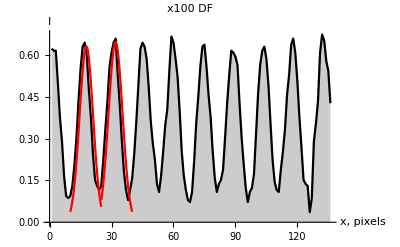

Левый пик:  | Estimate | Standard Error | t-Statistic | P-Value
a | 0.63101 | 0.0195445 | 32.2858 | 8.4614×10^-14
b | 7.78117 | 0.116994 | 66.5093 | 7.44822×10^-18
c | -3.27623 | 0.119859 | -27.334 | 7.15597×10^-13

Правый пик:  | Estimate | Standard Error | t-Statistic | P-Value
a | 0.646783 | 0.0245261 | 26.3712 | 1.13177×10^-12
b | 6.93087 | 0.148821 | 46.5719 | 7.51443×10^-16
c | 3.38576 | 0.156621 | 21.6175 | 1.42064×10^-11

```mathematica
img2DFSlice = 1 - ImageData[img2DFTrimmed][[60, All]];
f1L=10;
f1R=25;
f2L=25;
f2R=40;
img2DFSliceApproxPart1=img2DFSlice[[f1L;;f1R]];
img2DFSliceApproxPart2=img2DFSlice[[f2L;;f2R]];

img2DFSliceApproxPart1Fit=NonlinearModelFit[img2DFSliceApproxPart1,a Exp[-(x-b)^2/(2 c^2)],{a,b,c},x];
img2DFSliceApproxPartFit1Eq=img2DFSliceApproxPart1Fit["BestFit"]/.x->(x-f1L);

img2DFSliceApproxPart2Fit=NonlinearModelFit[img2DFSliceApproxPart2,a Exp[-(x-b)^2/(2 c^2)],{a,b,c},x];
img2DFSliceApproxPartFit2Eq=img2DFSliceApproxPart2Fit["BestFit"]/.x->(x-f2L);

Show[
ListPlot[img2DFSlice,PlotLabel->"x100 DF",Joined->True,PlotMarkers->None,Filling->Bottom,AxesLabel->{"x, pixels","I"}],(*Drawing slice*)
Plot[img2DFSliceApproxPartFit1Eq,{x,f1L,f1R},PlotStyle->Red],(*Drawing left peak*)
Plot[img2DFSliceApproxPartFit2Eq,{x,f2L,f2R},PlotStyle->Red](*Drawing right peak*)
]
Print["Левый пик: ",img2DFSliceApproxPart1Fit["ParameterTable"]]
Print["Правый пик: ",img2DFSliceApproxPart2Fit["ParameterTable"]]
```

Введем масштабирующий коэффициент (μm/pixel)

```mathematica
scaleExp2=ImageTrim[Import["2_2_x100_DF.png"],{{1884,20},{2028,60}}];
scalingCoefExp2 = Quantity[5, "Micrometers"]/ImageDimensions[scaleExp2][[1]]
```

5/146 µm

Оценим по снимку период структур

```mathematica
peak1DF = Around[(b /. img2DFSliceApproxPart1Fit["BestFitParameters"]) + f1L, img2DFSliceApproxPart1Fit["ParameterErrors"][[2]]];
peak2DF = Around[(b /. img2DFSliceApproxPart2Fit["BestFitParameters"]) + f2L, img2DFSliceApproxPart2Fit["ParameterErrors"][[2]]];
TS = (peak2DF - peak1DF)*scalingCoefExp2
```

(0.4850.006) µm

Аналогично оценим полуширину аппроксимированной структуры:

```mathematica
peak1DFWidth=2 √(2Log[2])*Around[Abs[c]/.img2DFSliceApproxPart1Fit["BestFitParameters"],img2DFSliceApproxPart1Fit["ParameterErrors"][[3]]];
peak2DFWidth=2 √(2Log[2])*Around[Abs[c]/.img2DFSliceApproxPart2Fit["BestFitParameters"],img2DFSliceApproxPart2Fit["ParameterErrors"][[3]]];
avgHalfWidthS=Mean[{peak1DFWidth,peak2DFWidth}]*scalingCoefExp2
```

(0.2690.008) µm

Установили, что разрешение для микроскопа в режим черного поля составляет около (0.485±0.006) μm.

### Гистограмма распределения по размерам частиц загрязнения

Получили изображение загрязненной части образца:

Снимок частиц загрязнения в режиме темного поля

Установим размер масштабирующего изображения

```mathematica
scale=ImageTrim[Import["3_x10_DF.png"],{{1884,20},{2028,60}}];
scalingCoef=Quantity[50,"Micrometers"]/ImageDimensions[scale][[1]]
```

25/73 µm

Преобразуем изображение в черно-белое и обрежем ненужные фрагменты

```mathematica
image=ImageTrim[Binarize[Import["3_x10_DF.png"]],{{0,0},{1720,1544}}]
```

-Graphics-

Составим таблицу с описанием параметров (изображение, длина, ширина и площадь эллипса, которым производится аппроксимация пятна).

```mathematica
dataset=ComponentMeasurements[image,{"Image","Length","Width","Area"},All,"Dataset",CornerNeighbors->True]
```

Dataset[<>]

По заданной таблице построим гистограмму с учетом масштабирующего коэффициента:

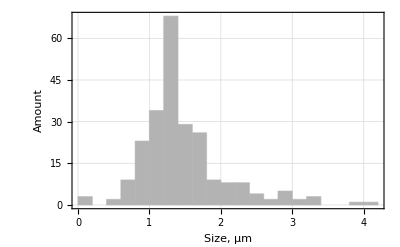

```mathematica
dustArray=Around[Mean[{Values[ComponentMeasurements[image,"Length"]],Values[ComponentMeasurements[image,"Width"]]}],1]*scalingCoef;
Histogram[dustArray,PlotRange->All,PlotTheme->"Detailed",FrameLabel->{"Size, μm","Amount"}]
```

### Определение разрешения, периода и скважности структуры по DIC изображению

Получили DIC изображения структур:

DIC снимок структуры T500 16-55-22

DIC снимок структуры T250nm_14-38-08

-Graphics-

DIC снимок структуры D500 15-39-57

Далее будем рассматривать структуру T500 16-55-22.

Увеличим рассматриваемый фрагмент

```mathematica
img4DIC = Import["4_x100_BF_DIC.png"];
img4DICTrimmed = ImageAdjust[Image[ImageData[ImageTrim[img4DIC, {{246, 587}, {246 + 134, 587 + 140}}]][[All, All, 2]]
   ]]
```

-Graphics-

Построим и срез и аппроксимируем два соседних пика.

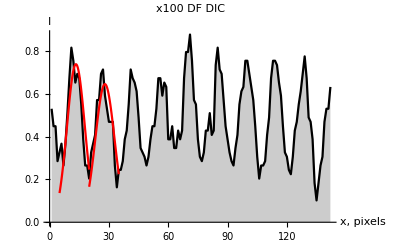

Левый пик:  | Estimate | Standard Error | t-Statistic | P-Value
a | 0.738768 | 0.0350608 | 21.0711 | 1.96465×10^-11
b | 8.30155 | 0.249766 | 33.2373 | 5.82494×10^-14
c | 4.51717 | 0.289976 | 15.5778 | 8.65304×10^-10

Правый пик:  | Estimate | Standard Error | t-Statistic | P-Value
a | 0.64558 | 0.0257291 | 25.0915 | 2.13583×10^-12
b | 7.97432 | 0.228113 | 34.9577 | 3.04314×10^-14
c | -4.83696 | 0.277053 | -17.4586 | 2.09445×10^-10

```mathematica
img4DICSlice = 1 - ImageData[img4DICTrimmed][[All, 60]];
f1LDIC=5;
f1RDIC=20;
f2LDIC=20;
f2RDIC=35;
img4DICSliceApproxPart1=img4DICSlice[[f1LDIC;;f1RDIC]];
img4DICSliceApproxPart2=img4DICSlice[[f2LDIC;;f2RDIC]];

img4DICSliceApproxPart1Fit=NonlinearModelFit[img4DICSliceApproxPart1,a Exp[-(x-b)^2/(2 c^2)],{a,b,c},x];
img4DICSliceApproxPartFit1Eq=img4DICSliceApproxPart1Fit["BestFit"]/.x->(x-f1LDIC);

img4DICSliceApproxPart2Fit=NonlinearModelFit[img4DICSliceApproxPart2,a Exp[-(x-b)^2/(2 c^2)],{a,b,c},x];
img4DICSliceApproxPartFit2Eq=img4DICSliceApproxPart2Fit["BestFit"]/.x->(x-f2LDIC);

Show[
ListPlot[img4DICSlice,PlotLabel->"x100 DF DIC",Joined->True,PlotMarkers->None,Filling->Bottom,AxesLabel->{"x, pixels","I"}],(*Drawing slice*)
Plot[img4DICSliceApproxPartFit1Eq,{x,f1LDIC,f1RDIC},PlotStyle->Red],(*Drawing left peak*)
Plot[img4DICSliceApproxPartFit2Eq,{x,f2LDIC,f2RDIC},PlotStyle->Red](*Drawing right peak*)
]
Print["Левый пик: ",img4DICSliceApproxPart1Fit["ParameterTable"]]
Print["Правый пик: ",img4DICSliceApproxPart2Fit["ParameterTable"]]
```

Коэффициент масштабирования:

```mathematica
scaleExp4 = ImageTrim[Import["4_x100_BF_DIC.png"], {{1884, 20}, {2028, 60}}];
scalingCoefExp4 = Quantity[5, "Micrometers"]/ImageDimensions[scaleExp4][[1]]
```

5/146 µm

Оценим по снимку период структур:

```mathematica
peak1DIC = Around[(b /. img4DICSliceApproxPart1Fit["BestFitParameters"]) + f1L, img4DICSliceApproxPart1Fit["ParameterErrors"][[2]]];
peak2DIC = Around[(b /. img4DICSliceApproxPart2Fit["BestFitParameters"]) + f2L, img4DICSliceApproxPart2Fit["ParameterErrors"][[2]]];
TDIC = (peak2DIC - peak1DIC)*scalingCoefExp4
```

(0.5020.012) µm

Аналогично оценим полуширину аппроксимированной структуры:

```mathematica
peak1DICWidth=2 √(2Log[2])*Around[Abs[c]/.img4DICSliceApproxPart1Fit["BestFitParameters"],img4DICSliceApproxPart1Fit["ParameterErrors"][[3]]];
peak2DICWidth=2 √(2Log[2])*Around[Abs[c]/.img4DICSliceApproxPart2Fit["BestFitParameters"],img4DICSliceApproxPart2Fit["ParameterErrors"][[3]]];
avgHalfWidthDIC=Mean[{peak1DICWidth,peak2DICWidth}]*scalingCoefExp4
```

(0.3770.016) µm

Установили, что разрешение для микроскопа в режим черного поля составляет около (0.502±0.012) μm.

Определим скважность структуры согласно формуле

S=T/τ

где T - период структур, τ - ширина отдельного пика. В результате:

```mathematica
S=TDIC/avgHalfWidthDIC
```

1.330.06

## Выводы

В режиме светлого поля различимы все структуры, однако с UV-фильтром разрешение незначительно уменьшается.

В режиме темного поля различима только одна из структур, однако с его помощью можно обнаружить частицы загрязнения.

Режим DIC так же позволяет разрешить все структуры.

Для режима DIC получили значение скважности: S=1.33±0.06.

Получили гистограмму размеров частиц загрязнения.